```mathematica
(*WYZNACZANIE POCHODNEJ*)
Clear[pochodna]
pochodna[f_,a_,n_]:=Module[{c,p},
p=D[f[x],{x,n}];
c=p/.{x->a};
Return[c]
]

(*PROGRAM METODY NEWTONA*)
Clear[newton]
newton[f_,a_,b_,ϵ_] := Module[{xs,xn,x0,m,z=1},
m=(a+b)/2;
If[pochodna[f,m,1]pochodna[f,m,2]<0,xn=a,xn=b];
xs=x0+2ϵ;
While[Abs[f[xn]]>ϵ, 
xs = xn; xn=xs- (f[xs]/ pochodna[f,xs,1]);
z++];
Print["Pierwiastkiem równania ",f[x],"=0 \njest liczba ", xn," otrzymana po ",z," krokach"]
]

(*TEST1*)
Clear[g]
```

```mathematica
g[x_] := E^(1-x^2) -.3;
newton[g,1,2,.0001]
```

Pierwiastkiem równania -0.3+ⅇ^(1-x^2)=0 
jest liczba 1.48458 otrzymana po 5 krokach

```mathematica
(*TEST2*)
Clear[h]
h[x_]:=ArcTan[x]-Log[E^(1-x^2)+3];
newton[h,.5,5,.0001]
```

Pierwiastkiem równania ArcTan[x]-Log[3+ⅇ^(1-x^2)]=0 
jest liczba 2.03053 otrzymana po 6 krokach

```mathematica
(*PROGRAM METODY NEWTONA(układ 2 równań)*)
Clear[newton2]
newton2[f_,g_,a_,ϵ_]:=Module[{xs=a+2ϵ,xn=a,c1,j,c,z=1},
While[Norm[{f[xs[[1]],xs[[2]]],g[xs[[1]],xs[[2]]]}]≥ϵ,
xs=xn;
j={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
c=j/.{x->xs[[1]],y->xs[[2]]};
c1=Inverse[c];
xn=xs-c1.{f[xs[[1]],xs[[2]]],g[xs[[1]],xs[[2]]]};
z++];
Print[" Rozwiązaniem równania jest ", xn," otrzymane po wykonaniu ",z," iteracji."]
]
```

```mathematica
(*TEST3*)
Clear[i,j]
i[x_,y_]:=x^2+2x y+1;
j[x_,y_]:=x^3-y^3-2;
a={3.,3.};
newton2[i,j,a,.001]
```

Rozwiązaniem równania jest {1.,-1.} otrzymane po wykonaniu 12 iteracji.

```mathematica
(*ZADANIE A*)
Clear[f1]
f1[x_]:=x^6-101
newton[f1,1,3.,10^(-10)]
```

Pierwiastkiem równania -101+x^6=0 
jest liczba 2.15801 otrzymana po 7 krokach

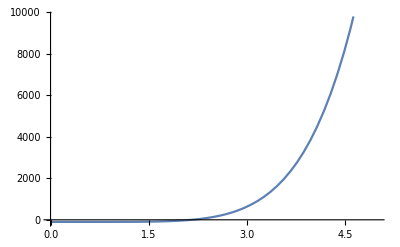

```mathematica
Plot[f1[x],{x,0,5}]
```

```mathematica
(*ZADANIE B*)
Clear[k,j,r,f2,f3]
```

Rozwiązaniem równania jest {2.38776,0.761224} otrzymane po wykonaniu 16 iteracji.

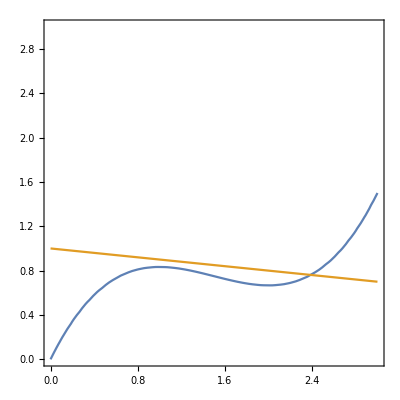

```mathematica
k=1;
j=1;
r=10;
f2[u_,i_]:=k*u*((u^2)/3-3u/2+2)-i;
f3[u_,i_]:=u/r+i-j;
newton2[f2,f3,{1.,1.},.01]
ContourPlot[{f2[x,y],f3[x,y]},{x,0,3},{y,0,3}]
```